## Comparison with existing functionals

### Contour integrals of arXiv:1910.12855

This refers to the following paper:
“A Basis of Analytic Functionals for CFTs in General Dimension”,
by Dalimil Mazac, Leonardo Rastelli, and Xinan Zhou

```mathematica
Hyperlink["https://arxiv.org/abs/1910.12855"]
```

https://arxiv.org/abs/1910.12855

#### Position-space blocks

```mathematica
G[hϕ_,h_][z_]:=z^(h-2hϕ)Hypergeometric2F1[h,h,2h,z]
```

#### Momentum-space blocks

```mathematica
S[hϕ_,h_,j_]:=Gamma[2h]/(Gamma[h]^2 Gamma[2hϕ-h]Gamma[h+2hϕ-1])1/((2hϕ-h+j)(h+2hϕ-1+j))
```

```mathematica
T[hϕ_,h_,j_]:=Gamma[h-2hϕ+1]/(Gamma[2hϕ-h]Gamma[h-2hϕ+1-j]Gamma[h+2hϕ+j])HypergeometricPFQ[{h,h,h-2hϕ+1,h+2hϕ-1},{2h,h-2hϕ+1-j,h+2hϕ+j},1]
```

#### Functionals defined with contour integrals

The integration kernel is given by eq. (2.17):

```mathematica
H[hϕ_,n_][z_]:=((-1)^n Pochhammer[2hϕ,n]^2)/(n!Pochhammer[4hϕ+n-1,n])1/z HypergeometricPFQ[{1,-n,4hϕ+n-1},{2hϕ,2hϕ},1/z]
```

We define a kernel with a different normalization:

```mathematica
H0[hϕ_,n_][z_]:=1/Gamma[2hϕ]^2 1/z HypergeometricPFQ[{1,-n,4hϕ+n-1},{2hϕ,2hϕ},1/z]
```

The ratio between the two is a constant:

```mathematica
(H[hϕ,n][z])/(H0[hϕ,n][z])==((-1)^n Gamma[2hϕ+n]^2)/(n!Pochhammer[4hϕ+n-1,n])//FullSimplify
```

True

The contour integral is given by eq. (2.30):

```mathematica
Sx[hϕ_,h_,j_]:=1/(2π)NIntegrate[H0[hϕ,j][1/2+I w]G[hϕ,h][1/2+I w],{w,-∞,∞}]//Chop
```

```mathematica
Tx[hϕ_,h_,j_]:=1/(2π)NIntegrate[H0[hϕ,j][1/2-I w]G[hϕ,h][1/2+I w],{w,-∞,∞}]//Chop
```

#### Numerical comparison

Compare the numerical integral with the function at random numerical values:

```mathematica
Table[Module[{hϕ,h,j},
hϕ=RandomReal[{0,2}];
h=RandomReal[{2,5}];
j=RandomInteger[{0,6}];
Sx[hϕ,h,j]/S[hϕ,h,j]],{100}]
```

```mathematica
Table[Module[{hϕ,h,j},
hϕ=RandomReal[{0,2}];
h=RandomReal[{2,5}];
j=RandomInteger[{0,6}];
Tx[hϕ,h,j]/T[hϕ,h,j]],{100}]
```

### Free fermion functionals of arXiv:1803.10233

This refers to the following paper:
“The Analytic Functional Bootstrap I: 1D CFTs and 2D S-Matrices”,
by Dalimil Mazac, and Miguel F. Paulos

```mathematica
Hyperlink["https://arxiv.org/abs/1803.10233"]
```

https://arxiv.org/abs/1803.10233

Eq. (4.24), up to a minus sign:

```mathematica
fβ[hϕ_][z_]:=-Gamma[4hϕ+4]/(2^(8hϕ+5)Gamma[hϕ+1]^2)(2z-1)/(z^(3/2)(z-1)^(3/2))(HypergeometricPFQRegularized[{-1/2,3/2,2hϕ+3/2},{hϕ+1,hϕ+2},-1/(4z(z-1))]+9/(16z(z-1))HypergeometricPFQRegularized[{1/2,5/2,2hϕ+5/2},{hϕ+2,hϕ+3},-1/(4z(z-1))])
```

Note: this can be rewritten as the derivative of a single generalized hypergeometric:

```mathematica
fβ[hϕ][z]==(3Gamma[4hϕ+3])/(2^(8hϕ+4)Gamma[hϕ+1]^2)z^(2hϕ/3)(z-1)^(2hϕ/3) D[1/(z^(2hϕ/3+1/2)(z-1)^(2hϕ/3+1/2))HypergeometricPFQRegularized[{-1/2,3/2,2hϕ+3/2},{hϕ+1,hϕ+2},-1/(4z(z-1))],z]//FullSimplify
```

True

Functional given by eq. (4.6):

```mathematica
ω[hϕ_,h_]:=2 Cos[π/2(h-2hϕ)]^2 NIntegrate[-fβ[hϕ][z](z-1)^(h-2hϕ)Hypergeometric2F1[h,h,2h,1-z],{z,1,∞}]
```

Alternative definition using integration by parts:

```mathematica
dω[hϕ_,h_][z_]=(3Gamma[4hϕ+3])/(2^(8hϕ+3)Gamma[hϕ+1]^2)Cos[π/2(h-2hϕ)]^2 1/(z^(2hϕ/3+1/2)(z-1)^(2hϕ/3+1/2))HypergeometricPFQRegularized[{-1/2,3/2,2hϕ+3/2},{hϕ+1,hϕ+2},-1/(4z(z-1))]D[z^(2hϕ/3)(z-1)^(h-4hϕ/3)Hypergeometric2F1[h,h,2h,1-z],z]//FullSimplify
```

1/(z^(3/2) Gamma[1+hϕ]^2)2^(-4-8 hϕ) (-1+z)^(-3/2+h-2 hϕ) Cos[1/2 (h-2 hϕ) π]^2 Gamma[2 h] Gamma[3+4 hϕ] (-4 hϕ (1+z) Hypergeometric2F1Regularized[h,h,2 h,1-z]+6 h z Hypergeometric2F1Regularized[h,1+h,2 h,1-z]) HypergeometricPFQRegularized[{-1/2,3/2,3/2+2 hϕ},{1+hϕ,2+hϕ},1/(4 z-4 z^2)]

```mathematica
ωalt[hϕ_,h_]:=NIntegrate[dω[hϕ,h][z],{z,1,∞}]
```

Numerical evaluation:

```mathematica
hϕ0=0.8;
```

```mathematica
ωdata=Monitor[Table[{h,ω[hϕ0,h]},{h,2hϕ0+2.25,10,0.1}],h];
```

Comparison with the numerical functionals:

```mathematica
SetDirectory[NotebookDirectory[]]
βFdata=Import["data/beta_F.csv"];
```

/home/marc/repos/CoBooM-2d

```mathematica
hϕtable=βFdata[[1,2;;]]
```

{0.01,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
htable=βFdata[[2;;,1]];
```

Normalize the two functionals at a given value:

```mathematica
h0=5.25;
```

```mathematica
{{hϕindex}}=Position[hϕtable,hϕ0]+1
{{hindex}}=Position[htable,h0]+1
```

{{18}}

{{527}}

```mathematica
n=Cases[ωdata,{h0,_}]⟦1,2⟧/βFdata[[hindex,hϕindex]]
```

0.152075

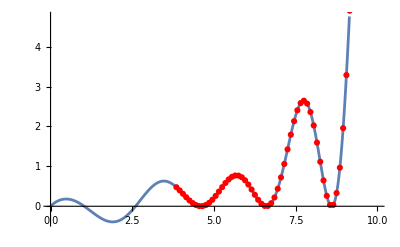

```mathematica
Show[ListLinePlot[{htable,n βFdata[[2;;,hϕindex]]}ᵀ],
ListPlot[ωdata,PlotStyle->Red]]
```